```mathematica
contour[pts_]:=Module[{vectors=Join@@(boxSides/@pts),
vertices,edges,
graph,tours},
vertices=Union[First/@vectors];
edges=vectors/.Thread[vertices->Range@Length@vertices];
graph=Graph[DirectedEdge@@@Complement[edges,Intersection[edges,Reverse/@edges]]];
tours=(First/@First@FindPostmanTour@Subgraph[graph,#])&/@ConnectedComponents@graph;
vertices⟦First@Select[tours,signarure[vertices⟦#⟧]&]⟧]
imageXY[{y_,x_}]:={x,size⟦2⟧+1-y};
boxSides[pt_]:=Partition[{pt+{-1/2,-1/2},pt+{1/2,-1/2},pt+{1/2,1/2},pt+{-1/2,1/2}},2,1,1];
signarure[path_]:=Positive@Total[Det/@Partition[path,2,1,1]]
```

```mathematica
image=ColorConvert[Import["http://cs629400.vk.me/v629400099/39bc2/Md48G41EPA8.jpg"],"Grayscale"]
```

-Graphics-

```mathematica
size=ImageDimensions[image];
minRegionArea=17;
edge1=EdgeDetect[image,4]
image2=Binarize[image,0.26]
components=MorphologicalComponents[image2,0,CornerNeighbors-> False];
count=ComponentMeasurements[components,"Count"];
areas=Union[Last/@count];
regionNames=First/@Select[count,Last[#]>minRegionArea&];
positions=Table[Position[components ImageData[MorphologicalPerimeter[image2,CornerNeighbors-> True],"Bit"],name],{name,regionNames}];
```

-Graphics-

-Graphics-

```mathematica
perimeters=ParallelMap[contour,positions];//AbsoluteTiming
```

{137.31,Null}

```mathematica
boundaries=Map[imageXY,perimeters,{2}];
colors=Join@@Table[ColorData[n,"ColorList"],{n,1,60}];
Graphics[Table[{colors⟦n⟧,Polygon[boundaries⟦n⟧]},{n,Length[boundaries]}],ImageSize->size]
```

-Graphics-

```mathematica
n=13;
linepts = contour[positions⟦n⟧];//AbsoluteTiming
```

{28.7132,Null}

```mathematica
tmp=Reverse@linepts[[#]]&/@Range[Length@linepts];
Ω=DiscretizeRegion[Polygon@tmp, MeshQualityGoal->1,MaxCellMeasure->0.5, AccuracyGoal->5]//AbsoluteTiming
```

{0.794881,-Graphics-}

```mathematica
sol00=NDSolveValue[{∇_{x,y}^2 u[x,y]==NeumannValue[0,True],DirichletCondition[u[x,y]==0,y≤ 10],DirichletCondition[u[x,y]==10,x==700]},u,{x,y}∈(Ω//Last)];//AbsoluteTiming
```

{1.72614,Null}

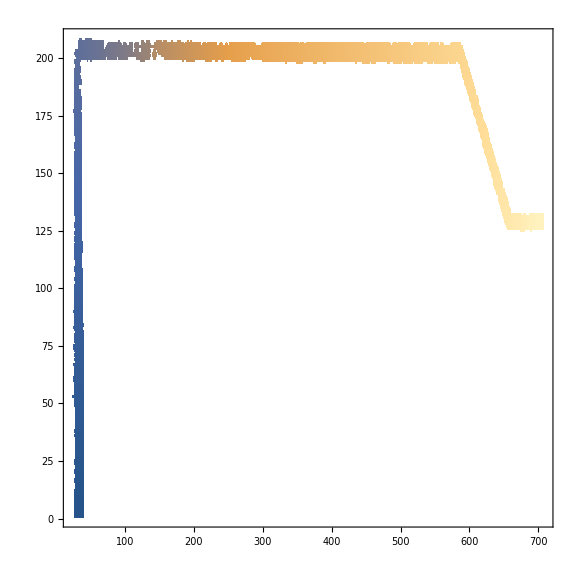
{2.52919,-Graphics-
-Graphics3D-}

```mathematica
Column@{
DensityPlot[sol00[x,y],{x,y}∈(Ω//Last),ImageSize->Large,PlotRange->Full],
Plot3D[sol00[x,y],{x,y}∈(Ω//Last),ImageSize->Large,PlotRange->Full]
}//AbsoluteTiming
```

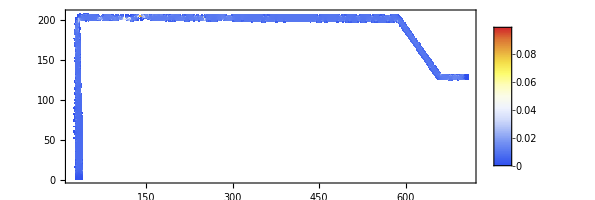
{4.79857,-Graphics-
-Graphics3D-}

```mathematica
uf=Grad[sol00[x,y],{x,y}];
Column@{
DensityPlot[Sqrt[uf[[1]]^2+uf[[2]]^2],{x,y}∈(Ω//Last),PlotLegends->Automatic,ColorFunction->"TemperatureMap",ImageSize->Full,AspectRatio->Automatic,PlotRange->All],
Plot3D[Sqrt[uf[[1]]^2+uf[[2]]^2],{x,y}∈(Ω//Last),PlotLegends->Automatic,ColorFunction->"TemperatureMap",ImageSize->Automatic,AspectRatio->Automatic]
}//AbsoluteTiming
```